```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
n=15; (* Points to sample along each connection *)
```

```mathematica
path=N@With[{Γ={0,0,0},X={0,1,0},W={1/2,1,0},L={1/2,1/2,1/2},K={3/4,3/4,0},U={1/4,1,1/4}},{L,K,U,W,Γ,X,W,L,Γ,K,U,X}]; (* The list of high-symmetry points *)
kPts=N@Subdivide[#1,#2,n]&@@@Partition[path,2,1]//Flatten[#,1]&//DeleteAdjacentDuplicates;(* List of n points sampled along each line of the path going through the high-symmetry points, it's literally the points generated by traversing the line, although not in equal steps *)
Length@kPts (* Total count of the sampling points *)
Graphics3D[{Point[#]&/@kPts,Line[path]},Axes->True]
```

166

-Graphics3D-

```mathematica
basis=N@{{1,-1,1},{1,1,-1},{-1,1,1}}; (* The basis for the G *)
G=Tuples[N@Range[-7,7],3].basis; (* All possible combinations that give the G points *)
Length@G (* Number of sampled points *)
(* 1BZ represented for a bcc lattice *)
eee=VoronoiMesh[G];
hm=HighlightMesh[eee,Style[2,Directive[Red]]];
eee=MeshRegion[MeshCoordinates[hm],MeshCells[hm,{3,"Interior"}]]
```

3375

-Graphics3D-

```mathematica
(*Export["~/Downloads/test3d.stl",MeshPrimitives[BoundaryMesh[eee],2]//RegionUnion,"STL"]*)
```

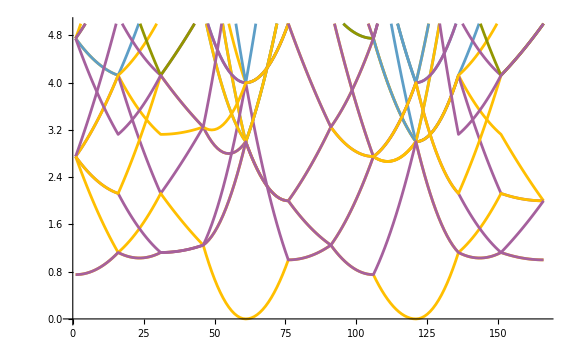

```mathematica
ens=With [{allCombs=Tuples[{kPts,G}]//Partition[#,Length@G]&},Norm[#1-#2]^2&@@@#&/@allCombs]//Transpose; (* Energy levels calculated along the path traced in the first Brillouin zone for a bcc lattice *)
ListLinePlot[ens,ImageSize->Large,PlotRange->{0,5}]
```

## 3D DOS (bulk)

```mathematica
firstBz=With[{G=Tuples[Range[-1,1],3].basis},Select[MeshPrimitives[VoronoiMesh[G],3],RegionMember[#,{0,0,0}]&]//First];
```

```mathematica
kPts=RandomPoint[firstBz,10^3];
Graphics3D[{Style[firstBz,Opacity[0.7]],Point@kPts}]
RegionMeasure[firstBz]
```

-Graphics3D-

4.

```mathematica
(*Export["~/Downloads/firstBz.stl",firstBz,"STL"]*)
```

```mathematica
G=Tuples[N@Range[-7,7],3].basis; (* All possible combinations that give the G points *)
allCombs=Tuples[{kPts,G}]//Partition[#,Length@G]&;
eVals=Norm[#1-#2]^2&@@@#&/@allCombs//Transpose;
```

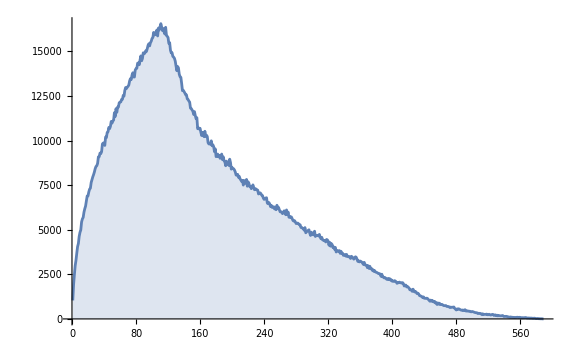

```mathematica
(* Plot of the density of states as a function of energy *)
Show[BinCounts[Flatten@eVals]//ListLinePlot[#,ImageSize->Large,Filling->Axis,PlotRange->All]&,Plot[dosFit["BestFit"],{x,0,130},PlotStyle->{Dashed,Orange,Thick}],PlotRange->All]
```

## 2D DOS part (quantum well)

```mathematica
n=1;
basis2d={{1,-1,1},{1,1,-1},{-1,1,1}}; (* The basis for the G *)
gen=Select[Tuples[Range[-9,9],3],Abs[#[[3]]]<=n&];
G2d=gen.basis2d;
vm=VoronoiMesh[G2d];
hm=HighlightMesh[vm,Style[2,Directive[Red]]];
vm=MeshRegion[MeshCoordinates[hm],MeshCells[hm,{3,"Interior"}]]
```

-Graphics3D-

```mathematica
(*Export["~/Downloads/test2d.stl",MeshPrimitives[BoundaryMesh[vm],2]//RegionUnion,"STL"]*)
```

```mathematica
allCombs=Tuples[{kPts,G2d}]//Partition[#,Length@G2d]&;
eVals=Norm[#1-#2]^2&@@@#&/@allCombs//Transpose;
```

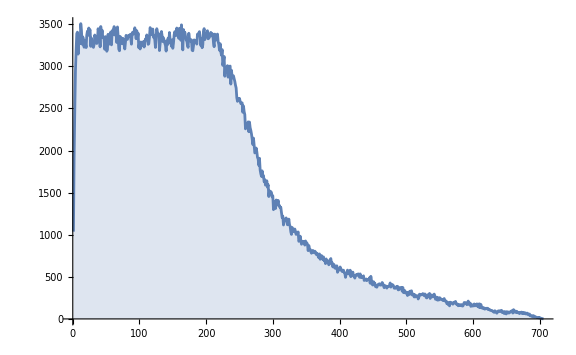

```mathematica
(* Plot of the density of states as a function of energy *)
BinCounts[Flatten@eVals]//ListLinePlot[#,ImageSize->Large,PlotRange->All,Filling->Axis]&
```

## 1D DOS part (quantum wire)

```mathematica
n=1
basis1d={{1,-1,1},{1,1,-1},{-1,1,1}}; (* The basis for the G *)
gen1=Select[Tuples[Range[-14,14],3],#[[3]]<=n&&#[[3]]>=-n&&#[[2]]<=n&&#[[2]]>=-n&];
G1d=gen1.basis1d;
vm1=VoronoiMesh[G1d];
hm=HighlightMesh[vm1,Style[2,Directive[Red]]];
vm1=MeshRegion[MeshCoordinates[hm],MeshCells[hm,{3,"Interior"}]]
```

1

-Graphics3D-

```mathematica
mp=MeshPrimitives[BoundaryMesh[vm1],2]//RegionUnion;
```

```mathematica
(*Export["~/Downloads/test1d.stl",mp, "STL"]*)
```

```mathematica
(*Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Report for the exam/1dlattPlt.pdf",vm1,ImageResolution->800]*)
```

```mathematica
allCombs=Tuples[{kPts,G1d}]//Partition[#,Length@G1d]&;
eVals=Norm[#1-#2]^2&@@@#&/@allCombs//Transpose;
```

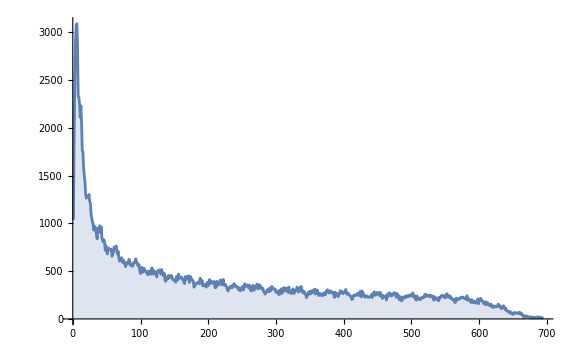

```mathematica
(* Plot of the density of states as a function of energy *)
BinCounts[Flatten@eVals]//ListLinePlot[#,ImageSize->Large,PlotRange->All,Filling->Axis]&
```

## 0D DOS part (quantum dots)

```mathematica
n=1
basis1d={{1,-1,1},{1,1,-1},{-1,1,1}}; (* The basis for the G *)
gen1=Select[Tuples[Range[-3,3],3],Abs[#[[3]]]<=n&&Abs[#[[2]]]<=n&&Abs[#[[1]]]<=n&];
G1d=gen1.basis1d;
vm1=VoronoiMesh[G1d];
hm=HighlightMesh[vm1,Style[2,Directive[Red]]];
vm1=MeshRegion[MeshCoordinates[hm],MeshCells[hm,{3,"Interior"}]]
```

1

-Graphics3D-

```mathematica
(*Printout3D[vm1]["FileName"][[1]]//CopyToClipboard*)
```

```mathematica
allCombs=Tuples[{kPts,G1d}]//Partition[#,Length@G1d]&;
eVals=Norm[#1-#2]^2&@@@#&/@allCombs//Transpose;
```

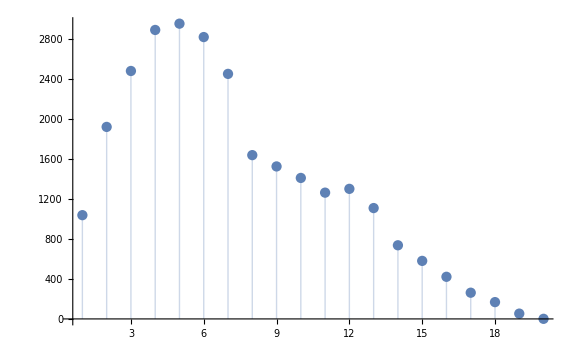

```mathematica
(* Plot of the density of states as a function of energy *)
BinCounts[Flatten@eVals]//ListPlot[#,ImageSize->Large,PlotRange->All,Filling->Axis]&
```